```mathematica
SetDirectory["C:\\Users\\benja\\OneDrive\\Documents\\GitHub\\KhovanovLaplacian\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing

ParentDirectory::nums: Argument File should be a positive machine-size integer, a nonempty string, or a File specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,WikiLink,mathematica}].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,QuantumGroups}].

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Loading KhovanovLaplacian`...

```mathematica
trefoilBen1= PD[X[1,4,2,5],X[5,2,6,3],X[3,6,4,1]]
trefoilBen2 = PD[X[1,4,2,5],X[7,2,8,3],X[3,8,4,9],X[5,10,6,1],X[6,10,7,9]]
trefoilBen3 = PD[X[4,1,5,2],X[2,5,3,6],X[6,3,1,4]]
```

PD[X[1,4,2,5],X[5,2,6,3],X[3,6,4,1]]

PD[X[1,4,2,5],X[7,2,8,3],X[3,8,4,9],X[5,10,6,1],X[6,10,7,9]]

PD[X[4,1,5,2],X[2,5,3,6],X[6,3,1,4]]

```mathematica
ParametricPlot3D[{Sin[u]+2*Sin[2*u],Sin[3*u],Cos[u]-2*Cos[2*u]},{u,0,2*Pi},ColorFunction->Function[{x,y,z,u},Hue[u]],AxesLabel->{x,y,z}]
(*trefoilBen1 and trefoilBen2 come from different rotations of the below knot, trefoilBen3 is from the braid diagram sigma_1^3*)
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u]+2*Sin[2*u],Sin[3*u],-Cos[u]+2*Cos[2*u]},{u,0,2*Pi},ColorFunction->Function[{x,y,z,u},Hue[u]],AxesLabel->{x,y,z}]
ParametricPlot[{Sin[u]+2*Sin[2*u],-Cos[u]+2*Cos[2*u]},{u,0,2*Pi},ColorFunction->Function[{x,z,u},Hue[u]],AxesLabel->{x,z}]
ParametricPlot[{Sin[u]+2*Sin[2*u],Sin[3*u]},{u,0,2*Pi},ColorFunction->Function[{x,y,u},Hue[u]],AxesLabel->{x,y}]
```

-Graphics3D-

-Graphics-

-Graphics-

PD[X[4,1,5,2],X[2,5,3,6],X[6,3,1,4]]

PD[X[8,2,9,1],X[2,8,3,7],X[3,12,4,13],X[4,12,5,11],X[10,6,11,5],X[6,14,7,13],X[9,14,10,1]]

PD[X[1,7,2,6],X[2,9,3,10],X[3,9,4,8],X[7,5,8,4],X[5,1,6,10]]

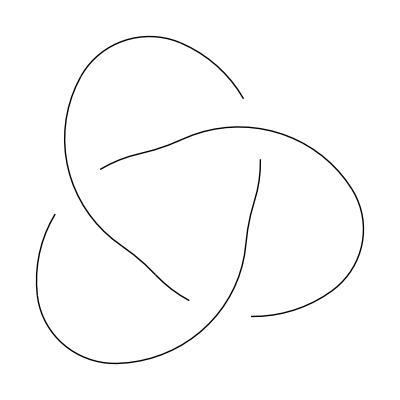

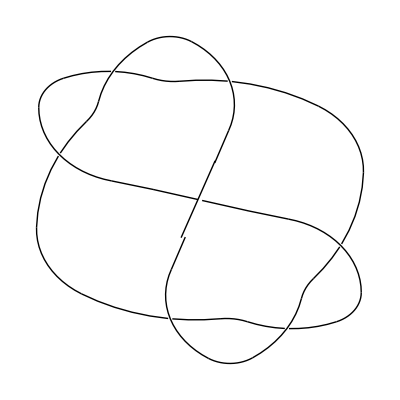

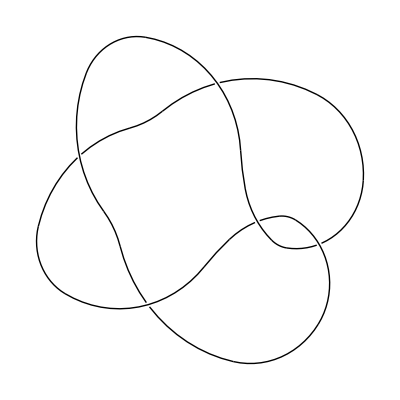

```mathematica
trefoilRight1 = PD[X[4,1,5,2],X[2,5,3,6],X[6,3,1,4]]
trefoilRight2 = PD[X[8,2,9,1],X[2,8,3,7],X[3,12,4,13],X[4,12,5,11],X[10,6,11,5],X[6,14,7,13],X[9,14,10,1]]
trefoilRight3 = PD[X[1,7,2,6],X[2,9,3,10],X[3,9,4,8],X[7,5,8,4],X[5,1,6,10]]
Show[DrawPD[trefoilRight1]]
Show[DrawPD[trefoilRight2]]
Show[DrawPD[trefoilRight3]]
```

```mathematica
LapKh[trefoilBen1]
LapKh[trefoilBen2]
LapKh[trefoilBen3]
s1 = qSpectraAllEigs[trefoilBen1]
s2 = qSpectraAllEigs[trefoilBen2]
s3 = qSpectraAllEigs[trefoilBen3]
```

LapBetti[-3,-9] = 1

LapBetti[-3,-7] = 0

LapBetti[-3,-5] = 0

LapBetti[-3,-3] = 0

LapBetti[-2,-7] = 0

LapBetti[-2,-5] = 1

LapBetti[-2,-3] = 0

LapBetti[-1,-5] = 0

LapBetti[-1,-3] = 0

LapBetti[0,-5] = 0

LapBetti[0,-3] = 1

LapBetti[0,-1] = 1

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

LapBetti[-4,-9] = 0

LapBetti[-4,-7] = 0

LapBetti[-4,-5] = 0

LapBetti[-3,-9] = 1

LapBetti[-3,-7] = 0

LapBetti[-3,-5] = 0

LapBetti[-3,-3] = 0

LapBetti[-2,-9] = 0

LapBetti[-2,-7] = 0

LapBetti[-2,-5] = 1

LapBetti[-2,-3] = 0

LapBetti[-2,-1] = 0

LapBetti[-1,-7] = 0

LapBetti[-1,-5] = 0

LapBetti[-1,-3] = 0

LapBetti[-1,-1] = 0

LapBetti[0,-7] = 0

LapBetti[0,-5] = 0

LapBetti[0,-3] = 1

LapBetti[0,-1] = 1

LapBetti[0,1] = 0

LapBetti[1,-5] = 0

LapBetti[1,-3] = 0

LapBetti[1,-1] = 0

LapBetti[1,1] = 0

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

LapBetti[-3,-9] = 1

LapBetti[-3,-7] = 0

LapBetti[-3,-5] = 0

LapBetti[-3,-3] = 0

LapBetti[-2,-7] = 0

LapBetti[-2,-5] = 1

LapBetti[-2,-3] = 0

LapBetti[-1,-5] = 0

LapBetti[-1,-3] = 0

LapBetti[0,-5] = 0

LapBetti[0,-3] = 1

LapBetti[0,-1] = 1

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

qSpectraAllEigs[-3,-9] = {0.}

qSpectraAllEigs[-3,-7] = {4.,1.,1.}

qSpectraAllEigs[-3,-5] = {5.,2.,2.}

qSpectraAllEigs[-3,-3] = {3.}

qSpectraAllEigs[-2,-7] = {4.,1.,1.}

qSpectraAllEigs[-2,-5] = {6.,6.,5.,2.,2.,4.01155×10^-16}

qSpectraAllEigs[-2,-3] = {3.,3.,3.}

qSpectraAllEigs[-1,-5] = {6.,6.,3.}

qSpectraAllEigs[-1,-3] = {6.,3.,3.}

qSpectraAllEigs[0,-5] = {3.}

qSpectraAllEigs[0,-3] = {6.,0.}

qSpectraAllEigs[0,-1] = {0.}

{{{0.},{4.,1.,1.},{5.,2.,2.},{3.}},{{4.,1.,1.},{6.,6.,5.,2.,2.,4.01155×10^-16},{3.,3.,3.}},{{6.,6.,3.},{6.,3.,3.}},{{3.},{6.,0.},{0.}}}

qSpectraAllEigs[-4,-9] = {3.}

qSpectraAllEigs[-4,-7] = {9.,4.}

qSpectraAllEigs[-4,-5] = {8.}

qSpectraAllEigs[-3,-9] = {3.,2.,-3.92481×10^-17}

qSpectraAllEigs[-3,-7] = {9.,7.71838,7.33685,6.64374,5.23607,4.,3.79329,2.,1.93378,0.763932,0.573963}

qSpectraAllEigs[-3,-5] = {10.,9.28856,8.62481,8.28317,8.,5.8511,5.03603,3.21217,2.83924,2.,0.864921}

qSpectraAllEigs[-3,-3] = {6.,5.41421,2.58579}

qSpectraAllEigs[-2,-9] = {2.}

qSpectraAllEigs[-2,-7] = {7.71838,7.33685,6.73205,6.64374,5.23607,4.,4.,3.79329,3.26795,2.,1.93378,0.763932,0.573963}

qSpectraAllEigs[-2,-5] = {10.,10.,10.,9.39239,9.28856,8.82216,8.62481,8.33018,8.28317,8.23659,6.,5.8511,5.09662,5.03603,4.82821,4.30376,3.21217,3.09397,2.83924,2.,1.71568,1.18043,0.864921,-8.69476×10^-16}

qSpectraAllEigs[-2,-3] = {8.,7.71959,7.58423,6.59798,6.,5.70572,5.57096,5.41421,4.18542,3.10635,2.58579,1.71005,0.819705}

qSpectraAllEigs[-2,-1] = {3.}

qSpectraAllEigs[-1,-7] = {6.73205,4.,4.,4.,3.26795}

qSpectraAllEigs[-1,-5] = {10.,10.,9.39239,8.82216,8.33018,8.23659,8.,7.65109,6.44949,6.,6.,5.09662,4.82821,4.72611,4.30376,3.6228,3.09397,1.71568,1.55051,1.18043}

qSpectraAllEigs[-1,-3] = {9.65188,9.61889,9.,8.22739,8.,7.71959,7.58423,6.59798,5.84427,5.70572,5.57096,4.29024,4.18542,4.,3.10635,3.05706,2.61973,1.71005,1.69053,0.819705}

qSpectraAllEigs[-1,-1] = {5.81361,3.52932,3.,3.,1.65708}

qSpectraAllEigs[0,-7] = {4.}

qSpectraAllEigs[0,-5] = {8.,7.65109,6.44949,6.,6.,4.72611,3.6228,1.55051}

qSpectraAllEigs[0,-3] = {9.65188,9.61889,9.,8.38849,8.22739,5.84427,5.18728,4.29024,4.,3.42423,3.05706,2.61973,1.69053,2.04781×10^-15}

qSpectraAllEigs[0,-1] = {7.04892,5.81361,3.52932,3.,2.6431,2.30798,1.65708,1.73269×10^-16}

qSpectraAllEigs[0,1] = {1.}

qSpectraAllEigs[1,-5] = {6.}

qSpectraAllEigs[1,-3] = {8.38849,5.18728,3.42423}

qSpectraAllEigs[1,-1] = {7.04892,2.6431,2.30798}

qSpectraAllEigs[1,1] = {1.}

{{{3.},{9.,4.},{8.}},{{3.,2.,-3.92481×10^-17},{9.,7.71838,7.33685,6.64374,5.23607,4.,3.79329,2.,1.93378,0.763932,0.573963},{10.,9.28856,8.62481,8.28317,8.,5.8511,5.03603,3.21217,2.83924,2.,0.864921},{6.,5.41421,2.58579}},{{2.},{7.71838,7.33685,6.73205,6.64374,5.23607,4.,4.,3.79329,3.26795,2.,1.93378,0.763932,0.573963},{10.,10.,10.,9.39239,9.28856,8.82216,8.62481,8.33018,8.28317,8.23659,6.,5.8511,5.09662,5.03603,4.82821,4.30376,3.21217,3.09397,2.83924,2.,1.71568,1.18043,0.864921,-8.69476×10^-16},{8.,7.71959,7.58423,6.59798,6.,5.70572,5.57096,5.41421,4.18542,3.10635,2.58579,1.71005,0.819705},{3.}},{{6.73205,4.,4.,4.,3.26795},{10.,10.,9.39239,8.82216,8.33018,8.23659,8.,7.65109,6.44949,6.,6.,5.09662,4.82821,4.72611,4.30376,3.6228,3.09397,1.71568,1.55051,1.18043},{9.65188,9.61889,9.,8.22739,8.,7.71959,7.58423,6.59798,5.84427,5.70572,5.57096,4.29024,4.18542,4.,3.10635,3.05706,2.61973,1.71005,1.69053,0.819705},{5.81361,3.52932,3.,3.,1.65708}},{{4.},{8.,7.65109,6.44949,6.,6.,4.72611,3.6228,1.55051},{9.65188,9.61889,9.,8.38849,8.22739,5.84427,5.18728,4.29024,4.,3.42423,3.05706,2.61973,1.69053,2.04781×10^-15},{7.04892,5.81361,3.52932,3.,2.6431,2.30798,1.65708,1.73269×10^-16},{1.}},{{6.},{8.38849,5.18728,3.42423},{7.04892,2.6431,2.30798},{1.}}}

qSpectraAllEigs[-3,-9] = {0.}

qSpectraAllEigs[-3,-7] = {4.,1.,1.}

qSpectraAllEigs[-3,-5] = {5.,2.,2.}

qSpectraAllEigs[-3,-3] = {3.}

qSpectraAllEigs[-2,-7] = {4.,1.,1.}

qSpectraAllEigs[-2,-5] = {6.,6.,5.,2.,2.,4.01155×10^-16}

qSpectraAllEigs[-2,-3] = {3.,3.,3.}

qSpectraAllEigs[-1,-5] = {6.,6.,3.}

qSpectraAllEigs[-1,-3] = {6.,3.,3.}

qSpectraAllEigs[0,-5] = {3.}

qSpectraAllEigs[0,-3] = {6.,0.}

qSpectraAllEigs[0,-1] = {0.}

{{{0.},{4.,1.,1.},{5.,2.,2.},{3.}},{{4.,1.,1.},{6.,6.,5.,2.,2.,4.01155×10^-16},{3.,3.,3.}},{{6.,6.,3.},{6.,3.,3.}},{{3.},{6.,0.},{0.}}}

```mathematica
s1 == s3
s1 == s2
qSpectraAllEigs[trefoilBen1,-2,-5]
qSpectraAllEigs[trefoilBen2,-2,-5]
tb1 = qLapNew[trefoilBen1,-2,-5]
tb2 = qLapNew[trefoilBen2,-2,-5]
```

True

False

qSpectraAllEigs[-2,-5] = {6.,6.,5.,2.,2.,4.01155×10^-16}

{6.,6.,5.,2.,2.,4.01155×10^-16}

qSpectraAllEigs[-2,-5] = {10.,10.,10.,9.39239,9.28856,8.82216,8.62481,8.33018,8.28317,8.23659,6.,5.8511,5.09662,5.03603,4.82821,4.30376,3.21217,3.09397,2.83924,2.,1.71568,1.18043,0.864921,-8.69476×10^-16}

{10.,10.,10.,9.39239,9.28856,8.82216,8.62481,8.33018,8.28317,8.23659,6.,5.8511,5.09662,5.03603,4.82821,4.30376,3.21217,3.09397,2.83924,2.,1.71568,1.18043,0.864921,-8.69476×10^-16}

SparseArray[…]

SparseArray[…]

```mathematica
tb1 // MatrixForm
tb2 // MatrixForm
Tr[tb1]
Tr[tb2]
```

(3 | 2 | 0 | -1 | -1 | 0
2 | 4 | 0 | 0 | 0 | 0
0 | 0 | 4 | 2 | 0 | 0
-1 | 0 | 2 | 3 | -1 | 0
-1 | 0 | 0 | -1 | 3 | 2
0 | 0 | 0 | 0 | 2 | 4)

(6 | 2 | -1 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 5 | 4 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 7 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 6 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 4 | 5 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 7 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 6 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 3 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 6 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 7 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 4 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 5 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 6 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 7 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 6)

21

137

```mathematica
tb1 = qLapNew[trefoilBen1,-1,-5]
tb1 //MatrixForm
a = GetDQ[trefoilBen1, 0, -5];
b = GetDQ[trefoilBen1, -1, -5];
a // MatrixForm
b // MatrixForm
```

SparseArray[…]

(5 | 1 | -1
1 | 5 | 1
-1 | 1 | 5)

(1 | -1 | 1)

(1 | 1 | -1 | -1 | 0 | 0
1 | 1 | 0 | 0 | -1 | -1
0 | 0 | 1 | 1 | -1 | -1)

```mathematica
c = Transpose[a].a
f = b.Transpose[b]
c // MatrixForm
d // MatrixForm
c+f // MatrixForm
Eigenvalues[c+f]
```

SparseArray[…]

SparseArray[…]

(1 | -1 | 1
-1 | 1 | -1
1 | -1 | 1)

d

(5 | 1 | -1
1 | 5 | 1
-1 | 1 | 5)

{6,6,3}

```mathematica
aneg2 = CC[trefoilBen1,-2,-5]
aneg1 = CC[trefoilBen1,-1,-5]
a0 = CC[trefoilBen1,0,-5]
a1 = CC[trefoilBen1,1,-5]
```

{v[0,0,1] vm[2] vp[1],v[0,0,1] vm[1] vp[2],v[0,1,0] vm[2] vp[1],v[0,1,0] vm[1] vp[2],v[1,0,0] vm[3] vp[1],v[1,0,0] vm[1] vp[3]}

{v[0,1,1] vm[1],v[1,0,1] vm[1],v[1,1,0] vm[1]}

{v[1,1,1] vm[1] vm[2]}

{0}

```mathematica
d[trefoilBen1][#] &/@ aneg1
```

{v[1,1,1] vm[1] vm[2],-v[1,1,1] vm[1] vm[2],v[1,1,1] vm[1] vm[2]}

```mathematica
aneg2
d[trefoilBen1][#] &/@aneg2
```

{v[0,0,1] vm[2] vp[1],v[0,0,1] vm[1] vp[2],v[0,1,0] vm[2] vp[1],v[0,1,0] vm[1] vp[2],v[1,0,0] vm[3] vp[1],v[1,0,0] vm[1] vp[3]}

{v[0,1,1] vm[1]+v[1,0,1] vm[1],v[0,1,1] vm[1]+v[1,0,1] vm[1],-v[0,1,1] vm[1]+v[1,1,0] vm[1],-v[0,1,1] vm[1]+v[1,1,0] vm[1],-v[1,0,1] vm[1]-v[1,1,0] vm[1],-v[1,0,1] vm[1]-v[1,1,0] vm[1]}

### Compute a total boundary map for trefoil, not just quantum parts

```mathematica
KhBracket[trefoilBen1,2]
```

{v[0,1,1] vm[1],v[0,1,1] vp[1],v[1,0,1] vm[1],v[1,0,1] vp[1],v[1,1,0] vm[1],v[1,1,0] vp[1]}

```mathematica
KhBracket[trefoilBen1,3]
```

{v[1,1,1] vm[1] vm[2],v[1,1,1] vm[2] vp[1],v[1,1,1] vm[1] vp[2],v[1,1,1] vp[1] vp[2]}

```mathematica
d[trefoilBen1][#] &/@ KhBracket[trefoilBen1,2]
Length[KhBracket[trefoilBen1,2]]
Length[KhBracket[trefoilBen1,3]]
```

{v[1,1,1] vm[1] vm[2],v[1,1,1] vm[2] vp[1]+v[1,1,1] vm[1] vp[2],-v[1,1,1] vm[1] vm[2],-v[1,1,1] vm[2] vp[1]-v[1,1,1] vm[1] vp[2],v[1,1,1] vm[1] vm[2],v[1,1,1] vm[2] vp[1]+v[1,1,1] vm[1] vp[2]}

6

4

```mathematica
trefoilBen4 = PD[X[1,5,2,4],X[3,1,4,6],X[5,3,6,2]] (*this is a right-handed trefoil w/ standard diagram*)
KhBracket[trefoilBen4,0]
KhBracket[trefoilBen4,1]
d[trefoilBen4][#] &/@ KhBracket[trefoilBen4,0]
Length[KhBracket[trefoilBen4,0]]
Length[KhBracket[trefoilBen4,1]]
```

PD[X[1,5,2,4],X[3,1,4,6],X[5,3,6,2]]

{v[0,0,0] vm[1] vm[2],v[0,0,0] vm[2] vp[1],v[0,0,0] vm[1] vp[2],v[0,0,0] vp[1] vp[2]}

{v[0,0,1] vm[1],v[0,0,1] vp[1],v[0,1,0] vm[1],v[0,1,0] vp[1],v[1,0,0] vm[1],v[1,0,0] vp[1]}

{0,v[0,0,1] vm[1]+v[0,1,0] vm[1]+v[1,0,0] vm[1],v[0,0,1] vm[1]+v[0,1,0] vm[1]+v[1,0,0] vm[1],v[0,0,1] vp[1]+v[0,1,0] vp[1]+v[1,0,0] vp[1]}

4

6